```mathematica
(*5(a).Solve using Laplace Transform:d^2y/dt^2-3 dy/dt+2y=t^2,y(0)=2,y'(0)=1*)
eq=y''[t]-3 y'[t]+2 y[t]==t^2;

tm=LaplaceTransform[eq,t,s];

tn=Solve[tm,LaplaceTransform[y[t],t,s]]/.{y'[0]->1,y[0]->2}
```

{{LaplaceTransform[y[t],t,s]→(2-5 s^3+2 s^4)/(s^3 (2-3 s+s^2))}}

```mathematica
tp=tn[[1,1,2]]
```

(2-5 s^3+2 s^4)/(s^3 (2-3 s+s^2))

```mathematica
InverseLaplaceTransform[tp,s,t]
```

1/4 (7+4 ⅇ^t-3 ⅇ^(2 t)+6 t+2 t^2)

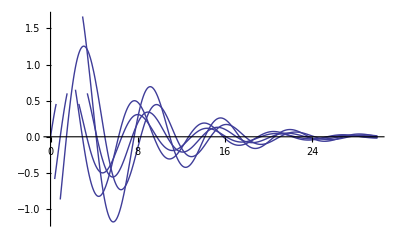

```mathematica
(*5(b).Solve d^2 y/dx^2+.3 dy/dx+sin y=0,y'(0)=1,y(0)=-2,-1,0,1,2,0≤x≤30 and sketch the graph of the solutions.*)Do[s=NDSolve[{y''[x]+.3 y'[x]+Sin[y[x]]==0,y[0]==i,y'[0]==1},y[x],{x,0,30}];
f[x_]=s[[1,1,2]];
g[i]=Plot[f[x],{x,0,30}],{i,-2,2}];

Show[{g[-2],g[-1],g[0],g[1],g[2]},PlotRange->All]
```